```mathematica
(* input rho1, th1, rho2 , rho1p *)
```

```mathematica
eps=1/4;
rho1=1+95/100eps;
th1=.;
rho2=1+eps;
rho1p=1+eps/2;
N[Sqrt[(3+rho1)/(1+3 rho1)]]
```

0.948264

```mathematica
vin=N[{√((1+3rho1)/(5+3 rho1+4 Cos[2 th1])),0}];
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=N[(3+rho1)/(1+3 rho1)vin.n1 n1+vin.t1 t1];
th21=N[ArcCos[Sqrt[-((3+rho1) (rho1+3 rho2) Cos[th1]^2)/(-5-6 rho1-5 rho1^2+4 (-1+rho1^2) Cos[2 th1])]]];
psi=N[ArcTan[Simplify[Abs[v1[[2]]]/v1[[1]]]]];
th2=psi+th21;
(* lower quantities *)
th1p=1/2 (ArcCos[(-3 rho1+3 rho1p+Cos[2 th1]+3 rho1p Cos[2 th1])/(1+3 rho1)]);
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=Simplify[(3+rho1p)/(1+3 rho1p)vin.n1p n1p+vin.t1p t1p];
th21p=ArcCos[Sqrt[-((3+rho1p) (rho1p+3 rho2) Cos[th1p]^2)/(-5-6 rho1p-5 rho1p^2+4 (-1+rho1p^2) Cos[2 th1p])]];
psip=ArcTan[Simplify[v1p[[2]]/v1p[[1]]]];
th2p=psip+th21p;
```

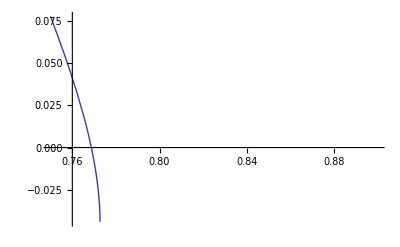

```mathematica
a0=(1+3 rho1) ((4 rho2+2 rho2 Cos[2 th1p]-rho2 Cos[2 (th1p-th2p)]-2 rho2 Cos[2 th2p]) (-2 (-1+rho1) (rho1+rho2) Sin[2 th1]+(rho1-rho2) ((-1+rho1) Sin[2 (th1-th2)]+2 (1+rho1) Sin[2 th2]))+(2 (-1+rho1) (rho1+rho2) Cos[2 th1]+(-1+rho1) (rho1-rho2) Cos[2 (th1-th2)]-2 (1+rho1) (2 (rho1+rho2)+(rho1-rho2) Cos[2 th2])) (2 rho2 Sin[2 th1p]+rho2 Sin[2 (th1p-th2p)]-2 rho2 Sin[2 th2p]));
a1=(1+3 rho1) ((4+4 rho2+2 Cos[2 th1p]-2 rho2 Cos[2 th1p]+Cos[2 (th1p-th2p)]+rho2 Cos[2 (th1p-th2p)]+2 Cos[2 th2p]-2 rho2 Cos[2 th2p]) (-2 (-1+rho1) (rho1+rho2) Sin[2 th1]+(rho1-rho2) ((-1+rho1) Sin[2 (th1-th2)]+2 (1+rho1) Sin[2 th2]))+(2 (-1+rho1) (rho1+rho2) Cos[2 th1]+(-1+rho1) (rho1-rho2) Cos[2 (th1-th2)]-2 (1+rho1) (2 (rho1+rho2)+(rho1-rho2) Cos[2 th2])) (2 Sin[2 th1p]-2 rho2 Sin[2 th1p]-Sin[2 (th1p-th2p)]-rho2 Sin[2 (th1p-th2p)]+2 Sin[2 th2p]-2 rho2 Sin[2 th2p]));
a2=(1+3 rho1) ((4-2 Cos[2 th1p]-Cos[2 (th1p-th2p)]+2 Cos[2 th2p]) (-2 (-1+rho1) (rho1+rho2) Sin[2 th1]+(rho1-rho2) ((-1+rho1) Sin[2 (th1-th2)]+2 (1+rho1) Sin[2 th2]))+(2 (-1+rho1) (rho1+rho2) Cos[2 th1]+(-1+rho1) (rho1-rho2) Cos[2 (th1-th2)]-2 (1+rho1) (2 (rho1+rho2)+(rho1-rho2) Cos[2 th2])) (-2 Sin[2 th1p]+Sin[2 (th1p-th2p)]+2 Sin[2 th2p]));
Plot[(-a1-√(a1^2-4 a0 a2))/(2 a2)-rho1p,{th1,.75,.9}]
```

```mathematica
(* change sign of square root if there is no zero*)
```

```mathematica
th1r=FindRoot[(-a1-√(a1^2-4 a0 a2))/(2 a2)-rho1p,{th1,3/4}]
```

{th1→0.768719}

```mathematica
(* choosing positive root here since gives sensible rho1p *)
```

```mathematica
(* now calculating velocity behind, above and below *)
```

```mathematica
th1=th1/.th1r
vin={√((1+3rho1)/(5+3 rho1+4 Cos[2 th1])),0};
n1={Cos[th1],-Sin[th1]};
t1={Sin[th1],Cos[th1]};
v1=Simplify[(3+rho1)/(1+3 rho1)vin.n1 n1+vin.t1 t1];
n2={Cos[th2],-Sin[th2]};
t2={Sin[th2],Cos[th2]};
v2=(3+rho2/rho1)/(1+3 rho2/rho1)v1.n2 n2+v1.t2 t2
```

0.768719

{0.690257,0.0384045}

```mathematica
t1p={Sin[th1p],Cos[th1p]};
n1p={Cos[th1p],-Sin[th1p]};
v1p=Simplify[(3+rho1p)/(1+3 rho1p)vin.n1p n1p+vin.t1p t1p];
t2p={Sin[th2p],Cos[th2p]};
n2p={Cos[th2p],-Sin[th2p]};
v2p=(3+rho2/rho1p)/(1+3 rho2/rho1p)v1p.n2p n2p+v1p.t2p t2p
```

{0.692103,0.0385072}

```mathematica
(v2p-v2)
```

{0.0018458,0.000102697}

```mathematica
(* check parallelism *)
```

```mathematica
v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]]
```

6.59195×10^-17

```mathematica
(* check all quantities are sensible *)
```

```mathematica
vin=N[{√((1+3rho1)/(5+3 rho1+4 Cos[2 th1])),0}]
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=N[(3+rho1)/(1+3 rho1)vin.n1 n1+vin.t1 t1]
N[-((3+rho1) (rho1+3 rho2) Cos[th1]^2)/(-5-6 rho1-5 rho1^2+4 (-1+rho1^2) Cos[2 th1])]
th21=N[ArcCos[Sqrt[-((3+rho1) (rho1+3 rho2) Cos[th1]^2)/(-5-6 rho1-5 rho1^2+4 (-1+rho1^2) Cos[2 th1])]]]
psi=N[ArcTan[Simplify[Abs[v1[[2]]]/v1[[1]]]]]
th2=psi+th21
```

{0.729885,0.}

{0.691874,-0.0367642}

0.545681

0.739653

0.0530872

0.79274

```mathematica
(* lower quantities *)
```

```mathematica
th1p=1/2 (ArcCos[(-3 rho1+3 rho1p+Cos[2 th1]+3 rho1p Cos[2 th1])/(1+3 rho1)])
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=Simplify[(3+rho1p)/(1+3 rho1p)vin.n1p n1p+vin.t1p t1p]
th21p=ArcCos[Sqrt[-((3+rho1p) (rho1p+3 rho2) Cos[th1p]^2)/(-5-6 rho1p-5 rho1p^2+4 (-1+rho1p^2) Cos[2 th1p])]]
psip=ArcTan[Simplify[v1p[[2]]/v1p[[1]]]]
th2p=psip+th21p
```

0.805731

{0.709879,0.0208366}

0.753079

0.0293439

0.782423

```mathematica
(*****************************************************)
```

```mathematica
(* HERE ARE ALL THE NUMERICAL VALUES FOR THE DENSITIES, ANGLES (IN RADIANS) AND VELOCITIES*)
```

```mathematica
(* Density in units of incoming unperturbed density, in regions 1, 2 and 1prime as labelled in diagram *)
```

```mathematica
N[rho1]
```

1.2375

```mathematica
N[rho2]
```

1.25

```mathematica
N[rho1p]
```

1.125

```mathematica
th1
```

0.768719

```mathematica
th2
```

0.79274

```mathematica
th1p
```

0.805731

```mathematica
th2p
```

0.782423

```mathematica
vin
```

{0.729885,0.}

```mathematica
v1
```

{0.691874,-0.0367642}

```mathematica
v2
```

{0.690257,0.0384045}

```mathematica
v1p
```

{0.709879,0.0208366}

```mathematica
v2p
```

{0.692103,0.0385072}

```mathematica
(* this is the velocity jump *)
```

```mathematica
v2p-v2
```

{0.0018458,0.000102697}

```mathematica
(* check that the two velocities on either side of the slip line are parallel *)
```

```mathematica
v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]]
```

6.59195×10^-17